## Ejercicio 3 - TP 01

Resolución de sistema lineal con RK4

Se parte de las siguientes ecuaciones
dx/dt= f(x,y)=f(x,y(t))
dy/dt= g(x,y)=g(x(t),y)
Aplicando el método RK4 a la primer ecuación diferencial se obtiene
x_(j+1)≈x_j+h/6(k_(1x)+2 k_(2x)+2 k_(3x)+k_(4x))
donde
k_(1x)=f(x_j,y(t_j))
k_x2=f(x_j+h/2 k_(1x),y(t_j+h/2))
k_x3=f(x_j+h/2 k_(2x),y(t_j+h/2))
k_x4=f(x_j+hk_(3x),y(t_j+h))

Se observa que para calcular x_(j+1)se necesita información sobre y. Lo mimso ocurre con y_(j+1). Este procedimiento recursivo no  permite avanzar a menos que se realicen algunas consideraciones. En primer lugar, es claro que  y(t_j)=y_j. En segundo lugar, dado que no se tiene información sobre y(t_j+h/2), se podría aproximar por el promedio y(t_j+h/2)≈(y_(j+1)+y_j)/2 donde y_(j+1)=y(t_j+h). Tampoco se tiene información de este último pero se puede aproximar por el método de Euler y_(j+1)≈y_j+h g(x_j,y_j) aprovechando la segunda ecuación diferencial.
En base a esto
k_(1x)=f(x_j,y_j)
k_x2=f(x_j+h/2 k_(1x),y_j+ h/2 g(x_j,y_j))
k_x3=f(x_j+h/2 k_(2x),y_j+ h/2 g(x_j,y_j))
k_x4=f(x_j+hk_(3x),y_j+h g(x_j,y_j))
Análogamente empleando la segunda ecuación diferencial
y_(j+1)≈y_j+h/6(k_(1y)+2 k_(2y)+2 k_(3y)+k_(4y))
donde
k_(1y)=g(x_j,y_j)
k_x2=g(x_j+h/2 f(x_j,y_j),y_j+h/2 k_(1y))
k_x3=f(x_j+h/2 f(x_j,y_j),y_j+ h/2 k_(2y))
k_x4=f(x_j+h f(x_j,y_j),y_j+h k_(3y))
Cabe aclarar que el método descripto anteriormente es una variante de RK4 dadas las aproximaciones realizadas.

```mathematica
(*Defino la función RK4 que toma como entrada los valores x_j e y_j, las funciones f(x,y) y g(x,y) del conjunto de ecuaciones diferenciales y el "paso" h*)
(*Defino las cosas devuelta pero más lindo:*)
RK4[x_,y_,f_,g_,h_]=Module[{kx1,kx2,kx3,kx4,ky1,ky2,ky3,ky4},
kx1:=f[x,y];
kx2 :=f[x+0.5h kx1, y + 0.5 h g[x,y]];
kx3:=f[x+0.5 h kx2,y+0.5 h g[x,y]];
kx4:=f[x+h kx3,y + h g[x,y]];
ky1:=g[x,y];
ky2:=g[x+0.5h f[x,y], y + 0.5 h ky1];
ky3:=g[x+0.5 h f[x,y],y+0.5 h ky2];
ky4:=g[x+h f[x,y],y + h ky3];
{x + h/6(kx1+ 2 kx2 + 2kx3 + kx4), y + h/6(ky1 + 2 ky2+ 2ky3+ ky4)}
];
(*Defino las funciones f y g donde las ctes a y b quedan aún sin definir*)
f[x_,y_] :=a-(b+1) x + x^2 y ; (*función de EDO*)
g[x_,y_]:= b x - x^2 y; (*función de EDO*)
```

Las iteraciones se detienen si se cumplen una de dos condiciones:
(1) El error en x e y estimados como la diferencia entre un valor y el siguiente para cada variable, es menor a una toleracia global “tolg” en ambos casos.
(2) Se llega a un número máximo de iteraciones “jmax”
Es claro que si se cumple (1) se está en presencia de un equilibrio estable. Mientras que si se cumple (2) para jmax “tan grande como se quiera”, de uno inestable.

Procedo a aplicar el método:

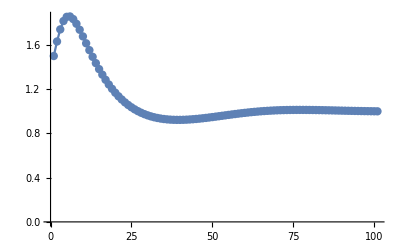

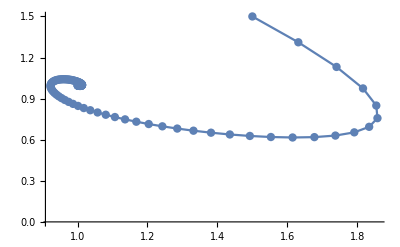

101

```mathematica
(*Condiciones iniciales*)
a = 1;
b = 1;
h = 0.1;
x0  =1.5;
y0 = 1.5;

tolg = 10^(-4);(*tolerancia general: me define cuándo voy a terminar de iterar*)
jmax = 100;
x = {x0}; y = {y0};
j = 1;
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++;
(*Armo un lazo While e itero hasta que se cumpla que la diferencia entre un valor y el siguiente sea menor a la tolerancia*)
condition = (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax); 
(*Pido que la diferencia sea menor para x e y porque quiero que se cumpla en ambos casos. Una decisión menos conservadora sería pedir que la norma de (x,y) sea menor a la tolerancia*)
While[condition == False,
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++; (*sumo un valor para hacer la próxima iteración*)
condition =  (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax);  (*evalúo nuevamente la condición para los datos que agregué*)
];
ListPlot[x, Joined->True, Mesh ->All,PlotRange->All]
ListPlot[Transpose[{x,y}],Joined->True, Mesh ->All,PlotRange->All]
Print[j]
(*PARA a=b=1, x0 = 1.5, y0 = 1.5, h = 1.0 NO FUNCIONA*)
(*Para a=1,b=3, x0 = 2, y0 = 2 (dentro del ciclo), h > 0.15 NO FUNCIONA*)
(*Para a=1,b=3, x0 = 0, y0 = 0 (fuera del ciclo), h > 0.16 NO FUNCIONA*)
```

Inciso a

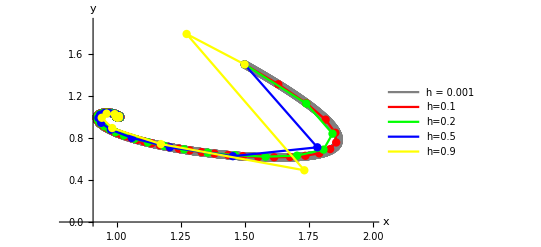

```mathematica
(*Condiciones iniciales*)
a = 1;
b = 1;
x0  =1.5;
y0 = 1.5;

(*solución g0*)
h = 0.001;

tolg = 10^(-5);(*tolerancia general: me define cuándo voy a terminar de iterar*)
jmax = 10000;
x = {x0}; y = {y0};
j = 1;
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++;
(*Armo un lazo While e itero hasta que se cumpla que la diferencia entre un valor y el siguiente sea menor a la tolerancia*)
condition = (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax); 
(*Pido que la diferencia sea menor para x e y porque quiero que se cumpla en ambos casos. Una decisión menos conservadora sería pedir que la norma de (x,y) sea menor a la tolerancia*)
While[condition == False,
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++; (*sumo un valor para hacer la próxima iteración*)
condition =  (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax);  (*evalúo nuevamente la condición para los datos que agregué*)
];
g0 = ListPlot[Transpose[{x,y}],Joined->True,Mesh->All,PlotRange->All, PlotLegends->{"h = 0.001"}, PlotStyle->Gray];

(*g1*)
h = 0.1;

tolg = 10^(-5);(*tolerancia general: me define cuándo voy a terminar de iterar*)
jmax = 10000;
x = {x0}; y = {y0};
j = 1;
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++;
(*Armo un lazo While e itero hasta que se cumpla que la diferencia entre un valor y el siguiente sea menor a la tolerancia*)
condition = (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax); 
(*Pido que la diferencia sea menor para x e y porque quiero que se cumpla en ambos casos. Una decisión menos conservadora sería pedir que la norma de (x,y) sea menor a la tolerancia*)
While[condition == False,
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++; (*sumo un valor para hacer la próxima iteración*)
condition =  (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax);  (*evalúo nuevamente la condición para los datos que agregué*)
];
g1 = ListPlot[Transpose[{x,y}],Joined->True,Mesh->All,PlotRange->All, PlotLegends->{"h=0.1"}, PlotStyle->Red];

(*g2*)
h = 0.2;

tolg = 10^(-5);(*tolerancia general: me define cuándo voy a terminar de iterar*)
jmax = 10000;
x = {x0}; y = {y0};
j = 1;
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++;
(*Armo un lazo While e itero hasta que se cumpla que la diferencia entre un valor y el siguiente sea menor a la tolerancia*)
condition = (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax); 
(*Pido que la diferencia sea menor para x e y porque quiero que se cumpla en ambos casos. Una decisión menos conservadora sería pedir que la norma de (x,y) sea menor a la tolerancia*)
While[condition == False,
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++; (*sumo un valor para hacer la próxima iteración*)
condition =  (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax);  (*evalúo nuevamente la condición para los datos que agregué*)
];
g2 = ListPlot[Transpose[{x,y}],Joined->True,Mesh->All,PlotRange->All, PlotLegends->{"h=0.2"}, PlotStyle->Green];

(*g3*)
h = 0.5;

tolg = 10^(-5);(*tolerancia general: me define cuándo voy a terminar de iterar*)
jmax = 10000;
x = {x0}; y = {y0};
j = 1;
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++;
(*Armo un lazo While e itero hasta que se cumpla que la diferencia entre un valor y el siguiente sea menor a la tolerancia*)
condition = (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax); 
(*Pido que la diferencia sea menor para x e y porque quiero que se cumpla en ambos casos. Una decisión menos conservadora sería pedir que la norma de (x,y) sea menor a la tolerancia*)
While[condition == False,
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++; (*sumo un valor para hacer la próxima iteración*)
condition =  (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax);  (*evalúo nuevamente la condición para los datos que agregué*)
];
g3 = ListPlot[Transpose[{x,y}],Joined->True,Mesh->All,PlotRange->All, PlotLegends->{"h=0.5"}, PlotStyle->Blue];

(*g4*)
h = 0.9;

tolg = 10^(-5);(*tolerancia general: me define cuándo voy a terminar de iterar*)
jmax = 10000;
x = {x0}; y = {y0};
j = 1;
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++;
(*Armo un lazo While e itero hasta que se cumpla que la diferencia entre un valor y el siguiente sea menor a la tolerancia*)
condition = (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax); 
(*Pido que la diferencia sea menor para x e y porque quiero que se cumpla en ambos casos. Una decisión menos conservadora sería pedir que la norma de (x,y) sea menor a la tolerancia*)
While[condition == False,
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++; (*sumo un valor para hacer la próxima iteración*)
condition =  (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax);  (*evalúo nuevamente la condición para los datos que agregué*)
];
g4= ListPlot[Transpose[{x,y}],Joined->True,Mesh->All,PlotRange->All, PlotLegends->{"h=0.9"}, PlotStyle->Yellow];

Show[{g0,g1,g2,g3,g4}, PlotRange->{{0.8,2},{0,1.9}},AxesLabel->{"x","y"}]
```

Reemplazando en el código anterior el caso a = b = 1 y usando diferentes pasos h = 0.1, 0.2, 0.5 y 1.0 se observa que las soluciones numéricas convergen al equilibrio x0* =, y0* = para los casos h = 0.1, 0.2 y 0.5. Mientras que para el caso h = 1.0 el programa registra un overflow por lo que se interpreta que no converge (o hay algún problema en el código). ¿Cómo se asegura que se llegó al equilibrio? Las iteraciones se detienen porque se cumplió la condición de tolerancia global.

### Inciso b

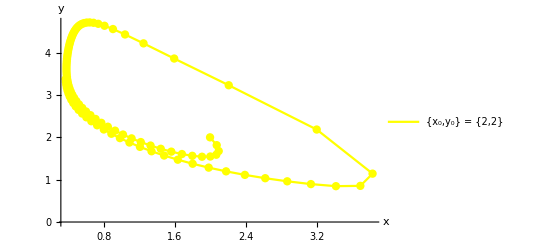

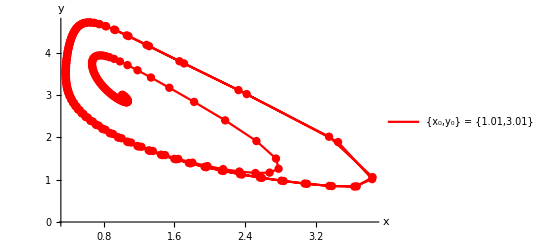

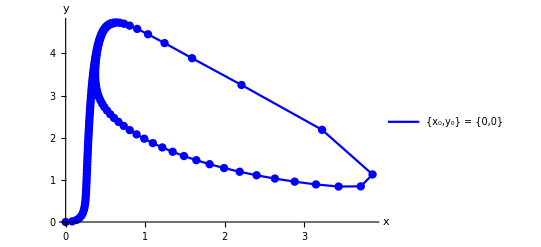

```mathematica
(*Condiciones iniciales*)
a = 1;
b = 3;
tolg = 10^(-4);(*tolerancia general: me define cuándo voy a terminar de iterar*)


(*Dentro del ciclo*)
h = 0.1;
x0  =2;
y0 = 2;

jmax = 100;
x = {x0}; y = {y0};
j = 1;
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++;
(*Armo un lazo While e itero hasta que se cumpla que la diferencia entre un valor y el siguiente sea menor a la tolerancia*)
condition = (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax); 
(*Pido que la diferencia sea menor para x e y porque quiero que se cumpla en ambos casos. Una decisión menos conservadora sería pedir que la norma de (x,y) sea menor a la tolerancia*)
While[condition == False,
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++; (*sumo un valor para hacer la próxima iteración*)
condition =  (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax);  (*evalúo nuevamente la condición para los datos que agregué*)
];
f1 = ListPlot[Transpose[{x,y}],Joined->True, Mesh ->All,PlotRange->All, PlotLegends->{"{x_0,y_0} = {2,2}"}, PlotStyle->{Yellow,Opacity[1]}];

(*Cerca del punto fijo*)
h = 0.1;
x0  =1.01;
y0 = 3.01;

jmax = 250;
x = {x0}; y = {y0};
j = 1;
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++;
(*Armo un lazo While e itero hasta que se cumpla que la diferencia entre un valor y el siguiente sea menor a la tolerancia*)
condition = (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax); 
(*Pido que la diferencia sea menor para x e y porque quiero que se cumpla en ambos casos. Una decisión menos conservadora sería pedir que la norma de (x,y) sea menor a la tolerancia*)
While[condition == False,
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++; (*sumo un valor para hacer la próxima iteración*)
condition =  (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax);  (*evalúo nuevamente la condición para los datos que agregué*)
];
f2 = ListPlot[Transpose[{x,y}],Joined->True, Mesh ->All,PlotRange->All, PlotLegends->{"{x_0,y_0} = {1.01,3.01}"}, PlotStyle->{Red,Opacity[1]}];

(*Fuera del ciclo*)
h = 0.1;
x0  =0;
y0 = 0;

jmax = 150;
x = {x0}; y = {y0};
j = 1;
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++;
(*Armo un lazo While e itero hasta que se cumpla que la diferencia entre un valor y el siguiente sea menor a la tolerancia*)
condition = (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax); 
(*Pido que la diferencia sea menor para x e y porque quiero que se cumpla en ambos casos. Una decisión menos conservadora sería pedir que la norma de (x,y) sea menor a la tolerancia*)
While[condition == False,
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++; (*sumo un valor para hacer la próxima iteración*)
condition =  (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax);  (*evalúo nuevamente la condición para los datos que agregué*)
];
f3 = ListPlot[Transpose[{x,y}],Joined->True, Mesh ->All,PlotRange->All, PlotLegends->{"{x_0,y_0} = {0,0}"}, PlotStyle->{Blue,Opacity[1]}];

Show[f1,AxesLabel->{"x","y"}]
Show[f2,AxesLabel->{"x","y"}]
Show[f3,AxesLabel->{"x","y"}]
```

```mathematica
a = 1;
b = 3;
x0 = 1.01;
y0 = 3.01;

(*solución m0*)
h = 0.001;

tolg = 10^(-5);(*tolerancia general: me define cuándo voy a terminar de iterar*)
jmax = 1000;
x = {x0}; y = {y0};
j = 1;
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++;
(*Armo un lazo While e itero hasta que se cumpla que la diferencia entre un valor y el siguiente sea menor a la tolerancia*)
condition = (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax); 
(*Pido que la diferencia sea menor para x e y porque quiero que se cumpla en ambos casos. Una decisión menos conservadora sería pedir que la norma de (x,y) sea menor a la tolerancia*)
While[condition == False,
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++; (*sumo un valor para hacer la próxima iteración*)
condition =  (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax);  (*evalúo nuevamente la condición para los datos que agregué*)
];
m0 = ListPlot[Transpose[{x,y}],Joined->True,Mesh->All,PlotRange->All, PlotLegends->{"Solucion"}, PlotStyle->{Gray,Opacity[0.5]}];

(*m1*)
h = 0.1;

tolg = 10^(-5);(*tolerancia general: me define cuándo voy a terminar de iterar*)
jmax = 200;
x = {x0}; y = {y0};
j = 1;
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++;
(*Armo un lazo While e itero hasta que se cumpla que la diferencia entre un valor y el siguiente sea menor a la tolerancia*)
condition = (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax); 
(*Pido que la diferencia sea menor para x e y porque quiero que se cumpla en ambos casos. Una decisión menos conservadora sería pedir que la norma de (x,y) sea menor a la tolerancia*)
While[condition == False,
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++; (*sumo un valor para hacer la próxima iteración*)
condition =  (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax);  (*evalúo nuevamente la condición para los datos que agregué*)
];
m1 = ListPlot[Transpose[{x,y}],Joined->True,Mesh->All,PlotRange->All, PlotLegends->{"h=0.1"}, PlotStyle->Red];

(*m2*)
h = 0.15;

tolg = 10^(-5);(*tolerancia general: me define cuándo voy a terminar de iterar*)
jmax = 300;
x = {x0}; y = {y0};
j = 1;
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++;
(*Armo un lazo While e itero hasta que se cumpla que la diferencia entre un valor y el siguiente sea menor a la tolerancia*)
condition = (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax); 
(*Pido que la diferencia sea menor para x e y porque quiero que se cumpla en ambos casos. Una decisión menos conservadora sería pedir que la norma de (x,y) sea menor a la tolerancia*)
While[condition == False,
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++; (*sumo un valor para hacer la próxima iteración*)
condition =  (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax);  (*evalúo nuevamente la condición para los datos que agregué*)
];
m2 = ListPlot[Transpose[{x,y}],Joined->True,Mesh->All,PlotRange->All, PlotLegends->{"h=0.15"}, PlotStyle->Green];

Show[{m1,m2}, PlotRange->{{-2,5},{0,7}},AxesLabel->{"x","y"}]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {{-24.7811,Overflow[]},{-5.6936088312094013468105929816538563041`15.954589770191005*^67218023941577,Overflow[]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::axorg: Value of option AxesOrigin -> {Overflow[],Overflow[]} is not Automatic or a valid 2D coordinate.

-Graphics-

Inciso b
Por otro lado, reemplazando por a = 1 y b = 3, se observa que el equilibrio es inestable, pues nunca se llega al equilibrio. Gráficamente, la solución es cíclica. Numéricamente, las iteraciones se detienen por la condición de máximo número de iteraciones.

## Ejercicio 4

Implementación de paso adaptativo

30

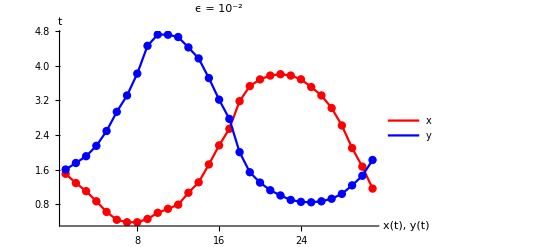

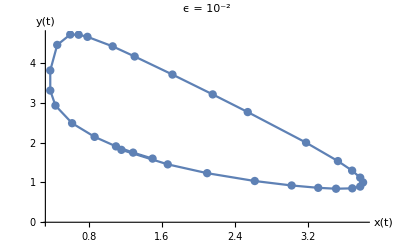

```mathematica
(*epsilon = 10^-2*)

(*Condiciones iniciales*)
a = 1;
b = 3;
h = 0.16; (*valor inicial de h*)
hs = {h}; (*guardo los valores de h usados*)
x0  =1.5;
y0 = 1.6;
tol = 10^(-2);

tolg = 10^(-7);(*tolerancia general: me define cuándo voy a terminar de iterar*)
jmax = 30; (*350*)
x = {x0}; y = {y0};
j = 1;
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++;
(*Armo un lazo While e itero hasta que se cumpla que la diferencia entre un valor y el siguiente sea menor a la tolerancia*)
condition = (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax); 
(*Pido que la diferencia sea menor para x e y porque quiero que se cumpla en ambos casos. Una decisión menos conservadora sería pedir que la norma de (x,y) sea menor a la tolerancia*)


While[condition == False,
{xnew1,ynew1} = RK4[x[[j]], y[[j]],f,g,h];

{xnew2pri,ynew2pri} = RK4[x[[j]], y[[j]],f,g,h/2];
{xnew2,ynew2} = RK4[xnew2pri, ynew2pri,f,g,h/2];

errorx = Abs[xnew2 - xnew1];
errory = Abs[ynew2 - ynew1];

caso1 = errorx>tol || errory > tol;
caso2 =(errorx> tol/2 && errorx<tol) || (errory> tol/2 && errory<tol);
caso3 = errorx<tol/2 && errory<tol/2;

If[caso1 == True,
h =h/1.5;
];
If[caso2 == True,
hs = Append[hs,h];
h =h;
x = Append[x,xnew2]; y = Append[y,ynew2];
j++;
];
If[caso3 == True,
hs = Append[hs,h];
h =1.5*h;
x = Append[x,xnew2]; y = Append[y,ynew2];
j++;
];
 (*sumo un valor para hacer la próxima iteración*)
condition =  (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax);  (*evalúo nuevamente la condición para los datos que agregué*)
];
Print[jmax];
n1 = ListPlot[x,Joined->True, Mesh ->All,PlotLegends->{"x"}, AxesLabel->{"x(t), y(t)","t"},PlotStyle->Red];
n2 = ListPlot[y,Joined->True, Mesh ->All,PlotLegends->{"y"}, AxesLabel->{"x(t), y(t)","t"},PlotStyle->Blue];
Show[{n1,n2},PlotRange->All, PlotLabel->"ϵ = 10^-2"]
ListPlot[Transpose[{x,y}],Joined->True, Mesh ->All,PlotRange->All, PlotLabel->"ϵ = 10^-2",  AxesLabel->{"x(t)","y(t)"}]
(*Para a=1,b=3,x0=0,y0=0 (fuera del ciclo),h_inicial=0.16,tol=10^-5,tolg=10^-7 se necesitan más de jmax=200000 pasos para que se de el primer ciclo.¿Cómo se adapta el paso en los régimenes de variación rápida del oscilador?Grafiquemos puntos de h vs variación definida como el módulo de la diferencia de dos puntos consecutivos.Es decir
variacion=variacion=Para a=1,b=3,x0=0,y0=0 (fuera del ciclo),h_inicial=0.16,tol=10^-2,tolg=10^-4 se necesitan jmax=2000 pasos aproximadamente para que se de el primer ciclo.*)
```

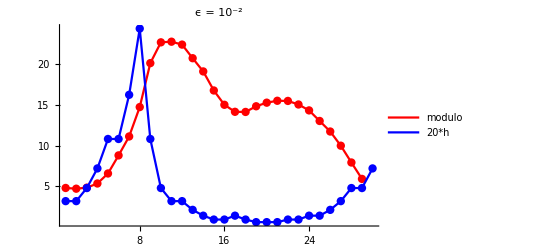

```mathematica
modulo = {};
Do[
modulo = Append[modulo, x[[j]]^2 + y[[j]]^2];
,{j,1,Length[x]-2}] 
n1 = ListPlot[x,Joined->True, Mesh ->All,PlotLegends->{"x"}, AxesLabel->{"x(t), y(t)","t"},PlotStyle->Red];
n2 = ListPlot[y,Joined->True, Mesh ->All,PlotLegends->{"y"}, AxesLabel->{"x(t), y(t)","t"},PlotStyle->Blue];
j1 = ListPlot[modulo,Joined->True, Mesh ->All,PlotRange->All, PlotLegends->{"modulo"}, PlotStyle->Red];
j2 = ListPlot[20*hs,Joined->True, Mesh ->All,PlotRange->All, PlotLegends->{"20*h"}, PlotStyle->Blue];
Show[{j1,j2},PlotLabel->"ϵ = 10^-2", PlotRange->All]

(*Cuando el modulo se mantiene más o menos cte, h crece (porque la difrencia es pequeña) o se mantiene cte (porque se está en el rango del enunciado). En cambio, cuando el modulo varia drásticamente, h decrece porque se está en la condición en la que el error es mayor a la tolerancia.*)
```

Cantidad de pasos: 7201

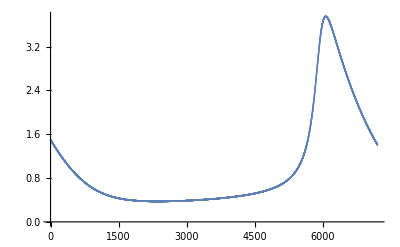

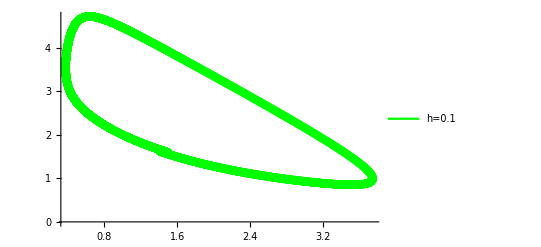

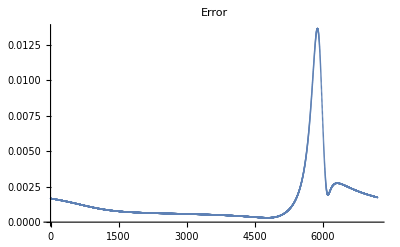

```mathematica
(*solución sin paso adaptativo*)
x0  =1.5;
y0 = 1.6;

h = 0.001;
tolg = 10^(-4);(*tolerancia general: me define cuándo voy a terminar de iterar*)
jmax = 7200;
x = {x0}; y = {y0};
j = 1;
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++;
(*Armo un lazo While e itero hasta que se cumpla que la diferencia entre un valor y el siguiente sea menor a la tolerancia*)
condition = (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax); 
(*Pido que la diferencia sea menor para x e y porque quiero que se cumpla en ambos casos. Una decisión menos conservadora sería pedir que la norma de (x,y) sea menor a la tolerancia*)
While[condition == False,
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++; (*sumo un valor para hacer la próxima iteración*)
condition =  (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax);  (*evalúo nuevamente la condición para los datos que agregué*)
];
Print["Cantidad de pasos: ",j]
ListPlot[x]
ListPlot[Transpose[{x,y}],Joined->True,Mesh->All,PlotRange->All, PlotLegends->{"h=0.1"}, PlotStyle->Green]
error = {};
Do[
error =Append[error,((x[[j+1]]-x[[j]])^2+ (y[[j+1]]-y[[j]])^2)^0.5];
,{j,1,Length[x]-2}] 
ListPlot[error, PlotRange->All, PlotLabel->"Error"]


(*Trabajando con las condiciones iniciales cerca de un punto del ciclo. Para la tol = 10^-2 se necesitan alrededor de 30 pasos para dar el ciclo en el caso adaptativo y alrededor de 7200 pasos para el caso no adaptativo*)
```

280

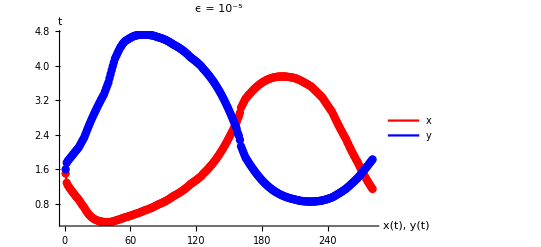

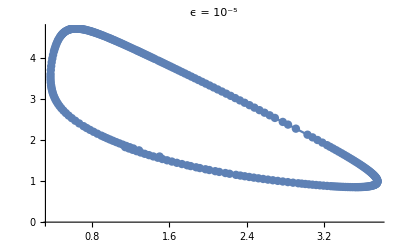

```mathematica
(*epsilon = 10^-5*)

(*Condiciones iniciales*)
a = 1;
b = 3;
h = 0.16; (*valor inicial de h*)
hs = {h}; (*guardo los valores de h usados*)
x0  =1.5;
y0 = 1.6;
tol = 10^(-5);

tolg = 10^(-7);(*tolerancia general: me define cuándo voy a terminar de iterar*)
jmax = 280;
x = {x0}; y = {y0};
j = 1;
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++;
(*Armo un lazo While e itero hasta que se cumpla que la diferencia entre un valor y el siguiente sea menor a la tolerancia*)
condition = (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax); 
(*Pido que la diferencia sea menor para x e y porque quiero que se cumpla en ambos casos. Una decisión menos conservadora sería pedir que la norma de (x,y) sea menor a la tolerancia*)


While[condition == False,
{xnew1,ynew1} = RK4[x[[j]], y[[j]],f,g,h];

{xnew2pri,ynew2pri} = RK4[x[[j]], y[[j]],f,g,h/2];
{xnew2,ynew2} = RK4[xnew2pri, ynew2pri,f,g,h/2];

errorx = Abs[xnew2 - xnew1];
errory = Abs[ynew2 - ynew1];

caso1 = errorx>tol || errory > tol;
caso2 =(errorx> tol/2 && errorx<tol) || (errory> tol/2 && errory<tol);
caso3 = errorx<tol/2 && errory<tol/2;

If[caso1 == True,
h =h/1.5;
];
If[caso2 == True,
hs = Append[hs,h];
h =h;
x = Append[x,xnew2]; y = Append[y,ynew2];
j++;
];
If[caso3 == True,
hs = Append[hs,h];
h =1.5*h;
x = Append[x,xnew2]; y = Append[y,ynew2];
j++;
];
 (*sumo un valor para hacer la próxima iteración*)
condition =  (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax);  (*evalúo nuevamente la condición para los datos que agregué*)
];
Print[jmax];
n1 = ListPlot[x,Joined->True, Mesh ->All,PlotLegends->{"x"}, AxesLabel->{"x(t), y(t)","t"},PlotStyle->Red];
n2 = ListPlot[y,Joined->True, Mesh ->All,PlotLegends->{"y"}, AxesLabel->{"x(t), y(t)","t"},PlotStyle->Blue];
Show[{n1,n2},PlotRange->All, PlotLabel->"ϵ = 10^-5"]
ListPlot[Transpose[{x,y}],Joined->True, Mesh ->All,PlotRange->All, PlotLabel->"ϵ = 10^-5"]
(*Para a=1,b=3,x0=0,y0=0 (fuera del ciclo),h_inicial=0.16,tol=10^-5,tolg=10^-7 se necesitan más de jmax=200000 pasos para que se de el primer ciclo.¿Cómo se adapta el paso en los régimenes de variación rápida del oscilador?Grafiquemos puntos de h vs variación definida como el módulo de la diferencia de dos puntos consecutivos.Es decir
variacion=variacion=Para a=1,b=3,x0=0,y0=0 (fuera del ciclo),h_inicial=0.16,tol=10^-2,tolg=10^-4 se necesitan jmax=2000 pasos aproximadamente para que se de el primer ciclo.*)
```

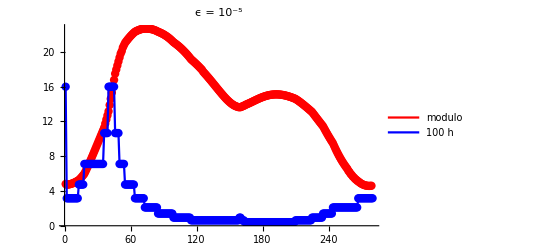

```mathematica
modulo = {};
vx = {}; vy = {};
Do[
(*AppendTo[vx,x[[j+1]] - x[[j]]];
AppendTo[vy,y[[j+1]] - y[[j]]];*)
modulo = Append[modulo, x[[j]]^2 + y[[j]]^2];
,{j,1,Length[x]-2}] 
n1 = ListPlot[x,Joined->True, Mesh ->All,PlotLegends->{"x"}, AxesLabel->{"x(t), y(t)","t"},PlotStyle->Red];
n2 = ListPlot[y,Joined->True, Mesh ->All,PlotLegends->{"y"}, AxesLabel->{"x(t), y(t)","t"},PlotStyle->Blue];
j1 = ListPlot[modulo,Joined->True, Mesh ->All,PlotRange->All, PlotLegends->{"modulo"}, PlotStyle->Red];
j2 = ListPlot[100*hs,Joined->True, Mesh ->All,PlotRange->All, PlotLegends->{"100 h"}, PlotStyle->Blue];
(*j3 = ListPlot[100*vx,Joined->True, Mesh ->All,PlotRange->All, PlotStyle->Green];
j4 = ListPlot[100*vy,Joined->True, Mesh ->All,PlotRange->All, PlotStyle->Yellow];*)
Show[{j1,j2},PlotLabel->"ϵ = 10^-5", PlotRange->All]

(*Cuando el modulo se mantiene más o menos cte, h crece (porque la difrencia es pequeña) o se mantiene cte (porque se está en el rango del enunciado). En cambio, cuando el modulo varia drásticamente, h decrece porque se está en la condición en la que el error es mayor a la tolerancia.*)
```

Cantidad de pasos: 9001

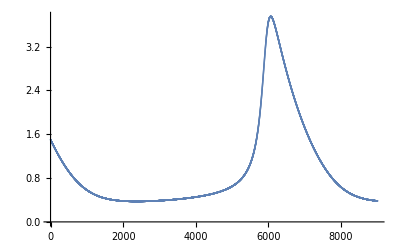

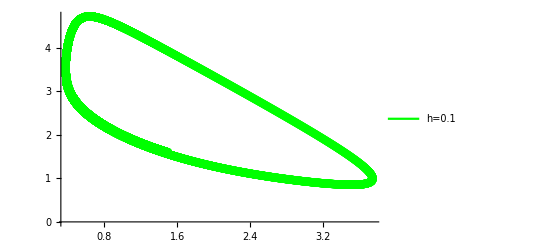

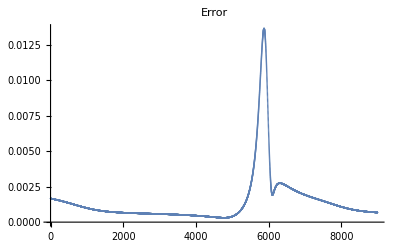

```mathematica
(*solución sin paso adaptativo*)
x0  =1.5;
y0 = 1.6;

h = 0.001; (*0.00001*)
tolg = 10^(-7);(*tolerancia general: me define cuándo voy a terminar de iterar*)
jmax = 9000; (*500000*)
x = {x0}; y = {y0};
j = 1;
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
x = Append[x,xnew];
y = Append[y,ynew];
j++;
(*Armo un lazo While e itero hasta que se cumpla que la diferencia entre un valor y el siguiente sea menor a la tolerancia*)
condition = (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax); 
(*Pido que la diferencia sea menor para x e y porque quiero que se cumpla en ambos casos. Una decisión menos conservadora sería pedir que la norma de (x,y) sea menor a la tolerancia*)
While[condition == False,
{xnew,ynew} = RK4[x[[j]], y[[j]],f,g,h];
AppendTo[x,xnew];
AppendTo[y,ynew];
j++; (*sumo un valor para hacer la próxima iteración*)
condition =  (Abs[x[[j]]-x[[j-1]]]<tolg && Abs[y[[j]]-y[[j-1]]]<tolg)|| (j > jmax);  (*evalúo nuevamente la condición para los datos que agregué*)
];
Print["Cantidad de pasos: ",j]
ListPlot[x]
ListPlot[Transpose[{x,y}],Joined->True,Mesh->All,PlotRange->All, PlotLegends->{"h=0.1"}, PlotStyle->Green]
error = {};
Do[
error =Append[error,((x[[j+1]]-x[[j]])^2+ (y[[j+1]]-y[[j]])^2)^0.5];
,{j,1,Length[x]-2}] 
ListPlot[error, PlotRange->All, PlotLabel->"Error"]
```